## Bidirectional Mother Machine

```mathematica
ClearAll["Global'*"]
Names["Global'*"]
```

{}

### Parameters and Problem

#### We separate our space into N ‘chunks’ that do not have to correspond to cells. Suppose our system is separable into 2 regions where each region has one type of cell. We write our master equation for the boundary when it is at the n^th cell: (dP(n,t))/dt=R_+(n-1)P(n-1,t)+R_-(n+1)P(n+1,t)-[R_+(n)+R_-(n)]P(n,t). What are R_+ and R_-? R_+=(∑_(i=0))^n W_+(i) is the sum of all the rates of cells i ≤ n grow to the right and R_-=(∑_(i=n))^N W_-(i) is the sum of rates that cells i > n grow to the left. W=f(i)=r/(1+(a(i(N_0-i)/N^2))^b)

```mathematica
fixb=2;
params={b->fixb,x0-> 2.0,c->1.0};
l0=c x0^(2b);
```

```mathematica
growthRateX=r/(1+c(x (x0-x))^b);
growthRate[y_,l0_,b_]:=1/(1+l0(y (1-y))^b);
(* y=x/x0, l0= c x0^(2b), pull r from everything *)
```

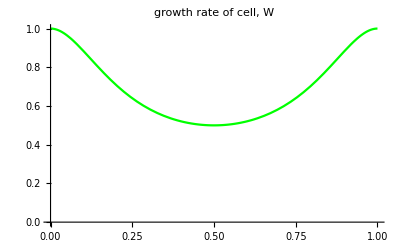

```mathematica
L=l0/.params;
Plot[growthRate[y,l0/.params,fixb],{y,0.,1},PlotRange-> {{0,1},{0,1}},PlotLabel->"growth rate of cell, W",PlotStyle-> Green]
```

#### The rate that a cell grows f(n) is dependent on the position in the channel, but we’re not too sure how... but here’s an approximation for W=W_++W_-. The rate of growth of a cell is the sum of the rate of growth to the right + rate of growth to the left. As such R=f(n)=R_++R_-=f(n)(n/N+(N-n)/N). One easy choice to find the rate of growth to the right is to simply assume the proportion of cells to the left determine how much it’ll move to the right and vice-versa. W_+(i)=f(i) i/N_0 W_-(i)=f(i) ((N_0-i)/N_0)

```mathematica
growthRateRight[y_,l0_,b_]:=y * growthRate[y,l0,b];
growthRateLeft[y_,l0_,b_]:=(1-y)* growthRate[y,l0,b];
```

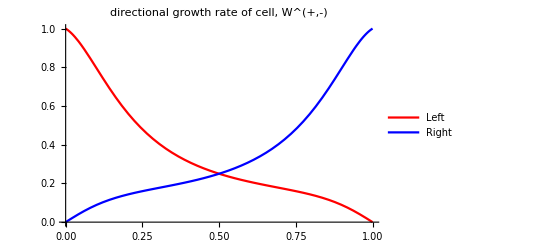

```mathematica
Plot[{growthRateLeft[y,l0/.params,fixb],growthRateRight[y,l0/.params,fixb]},{y,0.,1},PlotRange-> {{0,1},{0,1}},PlotLegends->{"Left","Right"},PlotLabel->"directional growth rate of cell, W^(+,-)",PlotStyle-> {Red,Blue}]
```

### Boundary Rates for fixed b

#### Now, we can find the rate of any boundary, j, moving to the right (or left) by summing over all the rate that any cell to the left (or right) divides to the right (or left): R_+(j)=(∑_(i=0))^j f(i) i/N R_-(j)=(∑_(i=j))^N f(i) (N-i)/N This is equivalent to an integral if we take the limit N→∞ .

#### These are the wrong expressions, but Anton did these integrals and I confirm they’re correct

```mathematica
(* gRRpar=FullSimplify[growthRateRight/y/.params];
gRLpar=FullSimplify[growthRateLeft/(1-y)/.params]; *)
```

```mathematica
(* reg=y∈ImplicitRegion[0≤y≤1,y];
Rplus=FullSimplify[Normal[Integrate[gRRpar,{y,0,y},Assumptions->{l>0,y∈Reals}]]];
Rminus=FullSimplify[Normal[Integrate[gRLpar,{y,y,1},Assumptions->{l>0,y∈Reals}]]]; *)
(* A=FullSimplify[ Rplus-Rminus];
B=FullSimplify[ Rplus+Rminus];
AoverB=A/B;*)
```

#### These are the correct expressions

```mathematica
GRRPAR[y_,l0_,b_]:=FullSimplify[growthRateRight[y,l0,b]];
GRLPAR[y_,l0_,b_]:=FullSimplify[growthRateLeft[y,l0,b]];
RPLUS[y_,l0_,b_]:=FullSimplify[Normal[Integrate[GRRPAR[y,l0,b],{y,0,y},Assumptions->{l0>0,y∈Reals}]]]; 
RMINUS[y_,l0_,b_]:=FullSimplify[Normal[Integrate[GRLPAR[y,l0,b],{y,y,1},Assumptions->{l0>0,y∈Reals}]]];
```

```mathematica
(* Need to evaluate these, take too long otherwise since integrals differ greatly depending on b=1,2,3... *)
Rplus=RPLUS[y,l,fixb]; (* 12 mins *)
Rminus=RMINUS[y,l,fixb] (* 13 mins *)
```

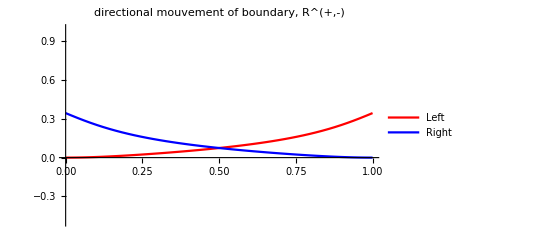

```mathematica
Plot[{Re[Rplus/.{l-> l0}/.params],Re[Rminus/.{l-> l0}/.params]},{y,0.,1},PlotRange-> {{0,1},{-0.5,1}},PlotLegends->{"Left","Right"},PlotLabel->"directional mouvement of boundary, R^(+,-)",PlotStyle-> {Red,Blue}]
(* RMINUS/.{l-> l0}/.params/.y-> 0.3
RPLUS/.{l-> l0}/.params/.y-> 0.6
Re[Rminus/.{l-> l0}/.params/.y-> 0.01]
Im[Rminus/.{l-> l0}/.params/.y-> 0.01]
Re[Rplus/.{l-> l0}/.params/.y-> 0.99]
Problem: Some of these expressions are complex. Why am I seeing this now? *)
```

#### Now we can expand our master to a FP equation and an equivalent backwards FP: (∂P(x,t|x_0,t_0))/(∂t)=A(x_0)(∂P)/(∂x_0)+(B(x_0))/2(∂^2 P)/(∂x_0^2)=L_x_0 P For the probability of exiting to the right P_R(x_0) or left P_L(x_0), solve L_x_0 P_R(x_0)=L_x_0 P_R(x_0)=0 with appropriate boundary condition.

```mathematica
A=Simplify[Rplus-Rminus];
B=Simplify[ Rplus+Rminus];
AOVERB=Simplify[A/B]; (* No time at all... maybe should try FullSimplify? *)
```

```mathematica
AOVERB/.l-> l0/.params/.y-> 0.7
```

0.61949-3.21722×10^-16 ⅈ

```mathematica
(* Unfortunately, can't seem to integrate this equation thus need to come up with another scheme to do this... P=Integrate[expfg,x] *)
(* EXPFG= FullSimplify[Exp[-2 Integrate[AOVERB,y,Assumptions->{l>0,y∈Reals}]]]; *)
```

```mathematica
Clear[phi,phi1,phi2,phi3,phi4,ProbR,ProbL,MFPT]
```

```mathematica
phi[x_?NumericQ,L_]:=phi[x,L]=Exp[-2 NIntegrate[ AOVERB/.{y-> Y,l->L},{Y,0,x}]];
phi1[x_?NumericQ,a_,L_]:=phi1[x,a,L]=Exp[2 NIntegrate[ AOVERB/.{y-> Y,l->L},{Y,a,x}]];
phi2[x_?NumericQ,a_,L_]:=phi2[x,a,L]=2 NIntegrate[ (phi1[y,a,L]/B)/.{y-> Y,l->L},{Y,a,x}];
phi3[x_?NumericQ,a_,l_]:=phi3[x,a,l]=NIntegrate[(1/phi1[y,a,l]),{y,a,x}];
phi4[x_?NumericQ,a_,l_]:=phi4[x,a,l]=NIntegrate[(phi2[y,a,l]/phi1[y,a,l]),{y,a,x}];
ProbR[x_?NumericQ,a_,b_,l_]:=NIntegrate[phi[y,l],{y,a,x}]/NIntegrate[phi[y,l],{y,a,b}];
ProbL[x_?NumericQ,a_,b_,l_]:=NIntegrate[phi[y,l]/.params,{y,x,b}]/NIntegrate[phi[y,l],{y,a,b}];
```

```mathematica
MFPT[y_?NumericQ,a_,b_,l_]:=(phi3[y,a,l]phi4[b,a,l]-phi3[b,a,l]phi4[y,a,l])/phi3[b,a,l]
```

#### Examples of P_(fix,right)(y_0) and P_(fix,left)(y_0)

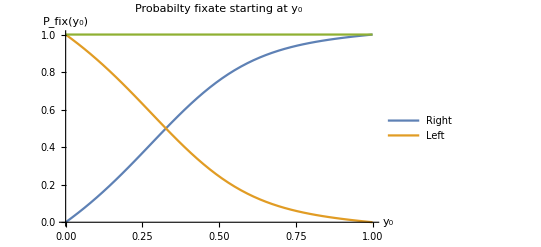

```mathematica
params1={b->fixb,x0-> 2.0,c->1.0};
Plot[{ProbR[x,0.0,1.0,l0/.params1],ProbL[x,0.0,1.0,l0/.params1],ProbR[x,0.0,1.0,l0/.params1]+ProbL[x,0.0,1.0,l0/.params1]},{x,0.0,1.0},PlotLabel->"Probabilty fixate starting at y_0",PlotLegends->{"Right","Left"},AxesLabel->{"y_0","P_fix(y_0)"}] (* like... 1 minute not even*)
```

#### Examples of the mean first passage time to fixate

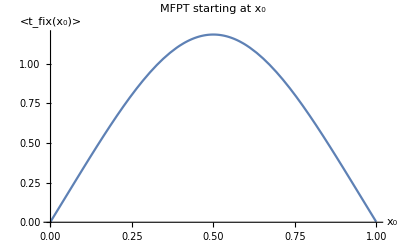

```mathematica
Plot[MFPT[y,0.0,1.0],{y,0.0,1.0},PlotLabel->"MFPT starting at y_0",AxesLabel->{"y_0","<t_fix(y_0)>"}] (* This is long ~25 mins *)
```

#### Ranges for P_(fix,right)(y_0) and P_(fix,left)(y_0) given different x_0 and c

```mathematica
paramsNoC={b->fixb,x0-> 2.0};
paramsNoY0={b->fixb,c-> 2.0};
```